## Question 1

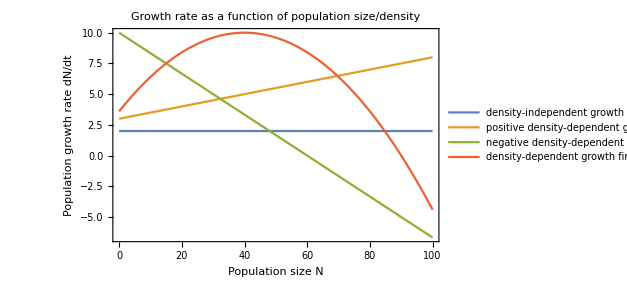

```mathematica
Plot[{2,1/20*x+3,10-1/6 x,-0.004(x-40)^2+10},{x,0,100},Frame->True,FrameLabel->{"Population size N","Population growth rate dN/dt"},PlotLabel->Style["Growth rate as a function of population size/density",18],PlotLegends->{"density-independent growth","positive density-dependent growth","negative density-dependent growth","density-dependent growth \nfirst positive, then negative"}]
```

```mathematica
logisticGrowthRate[n_,r_,k_]:=r*n(1-n/k)
```

```mathematica
alleeEffectGrowthRate[n_,u_,c_,v_]:=((u*n)/(v+n)-c*n)n
```

## Question 2

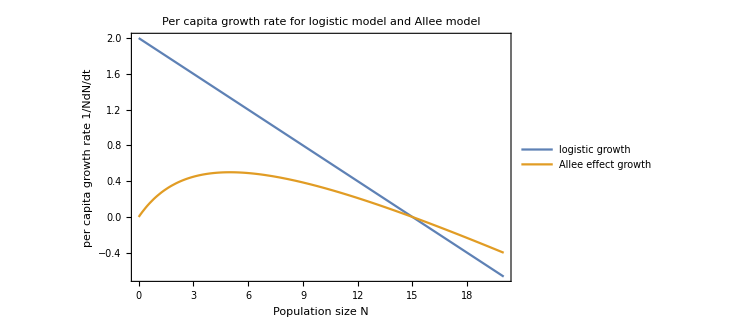

```mathematica
Plot[{1/n*logisticGrowthRate[n,2,15],1/n *alleeEffectGrowthRate[n,2,0.1,5]},{n,0,20},Frame->True,FrameLabel->{Style["Population size N",15],Style["per capita growth rate 1/NdN/dt",15]},PlotLabel->Style["Per capita growth rate for logistic model and Allee model",20],PlotLegends->{"logistic growth", "Allee effect growth"}]
```

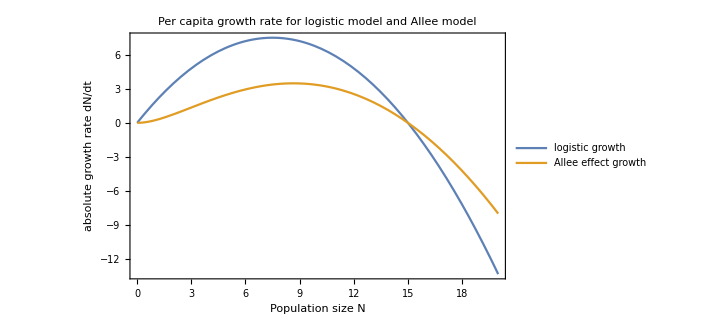

```mathematica
Plot[{logisticGrowthRate[n,2,15],alleeEffectGrowthRate[n,2,0.1,5]},{n,0,20},Frame->True,FrameLabel->{Style["Population size N",15],Style["absolute growth rate dN/dt",15]},PlotLabel->Style["Per capita growth rate for logistic model and Allee model",20],PlotLegends->{"logistic growth", "Allee effect growth"}]
```

Finding

```mathematica
Solve[D[logisticGrowthRate[n,2,15],n]==0]
```

{{n→15/2}}

```mathematica
logisticGrowthRate[7.5,2,15]//N
```

7.5

```mathematica
Solve[D[alleeEffectGrowthRate[n,2,0.1,5],n]==0&&n>0,n]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→8.66025}}

```mathematica
alleeEffectGrowthRate[8.66025,2,0.1,5]
```

3.48076

```mathematica
Solve[D[1/n*alleeEffectGrowthRate[n,2,0.1,5],n]==0&&n>0,n]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{n→5.}}

```mathematica
1/5*alleeEffectGrowthRate[5,2,0.1,5]
```

0.5

## Question 3

Ricker Model

Find N^* candidates

```mathematica
Solve[n==r*n*Exp[-b*n],n]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{n→0},{n→-Log[1/r]/b}}

```mathematica
ClearAll[f]
```

```mathematica
f[n_]:=r*f[n-1]*Exp[-b*f[n-1]]
```

```mathematica
D[r*x*Exp[-b*x],x]
```

ⅇ^(-b x) r-b ⅇ^(-b x) r x

Try the first fixed point

```mathematica
ⅇ^(-b x) r-b ⅇ^(-b x) r x/.x->0
```

r

```mathematica
ⅇ^(-b x) r-b ⅇ^(-b x) r x/.x->-Log[1/r]/b
```

1+Log[1/r]

```mathematica
Solve[Abs[1+Log[1/r]]==1&&r>0,r]
```

{{r→1},{r→ⅇ^2}}

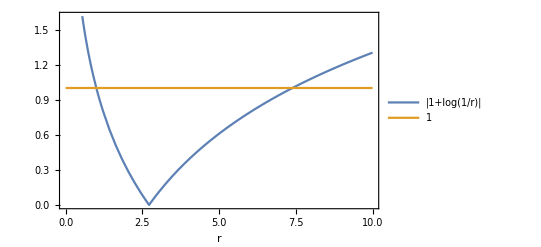

```mathematica
Plot[{Abs[1+Log[1/x]],1},{x,0,10},Frame->True,FrameLabel->{"r"},PlotLegends->{"|1+log(1/r)|","1"}]
```

Find the period-2 points

```mathematica
Solve[n==r^2 n*Exp[-b*n*(1+r*Exp[-b*n])]&&n>0,n]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[n==ⅇ^(-b n (1+ⅇ^(-b n) r)) n r^2&&n>0,n]